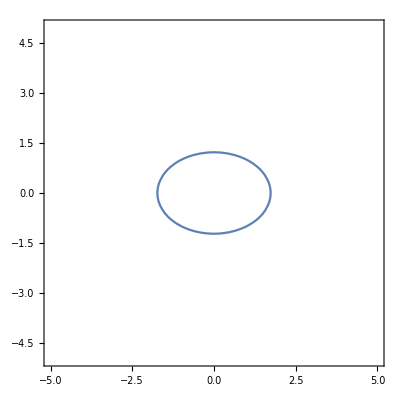

```mathematica
Исходные данные;
p=73;
a=25;
b=25;
n=8;

Задание 1;
ContourPlot[x^2+2*y^2==3, {x, -5, 5}, {y, -5,5}]
```

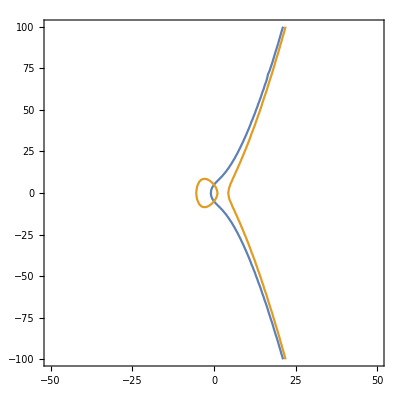

```mathematica
Задание 2;
ContourPlot[{y^2==x^3+a*x+b, y^2==x^3+(-a)*x+b},{x, -50, 50}, {y, -100, 100}]
```

```mathematica
Mod[4*a^3+27*b^2,p]≠0
```

True

```mathematica
Factor[x^3+a*x+b]
```

25+25 x+x^3

```mathematica
Задание 3;
Clear[x,y]; 
g1o = {x,y} /.Flatten[Table[ Solve[ {y^2== x^3+a*x + b, x==u, Modulus==p}, Reals],{u, 0, p-1}] ,1]
```

{{0,-5},{0,5},{1,-√51},{1,√51},{2,-√83},{2,√83},{3,-√127},{3,√127},{4,-3 √21},{4,3 √21},{5,-5 √11},{5,5 √11},{6,-√391},{6,√391},{7,-√543},{7,√543},{8,-√737},{8,√737},{9,-√979},{9,√979},{10,-5 √51},{10,5 √51},{11,-√1631},{11,√1631},{12,-√2053},{12,√2053},{13,-3 √283},{13,3 √283},{14,-√3119},{14,√3119},{15,-5 √151},{15,5 √151},{16,-√4521},{16,√4521},{17,-√5363},{17,√5363},{18,-√6307},{18,√6307},{19,-√7359},{19,√7359},{20,-5 √341},{20,5 √341},{21,-√9811},{21,√9811},{22,-3 √1247},{22,3 √1247},{23,-√12767},{23,√12767},{24,-√14449},{24,√14449},{25,-5 √651},{25,5 √651},{26,-√18251},{26,√18251},{27,-√20383},{27,√20383},{28,-√22677},{28,√22677},{29,-√25139},{29,√25139},{30,-5 √1111},{30,5 √1111},{31,-3 √3399},{31,3 √3399},{32,-√33593},{32,√33593},{33,-√36787},{33,√36787},{34,-√40179},{34,√40179},{35,-5 √1751},{35,5 √1751},{36,-√47581},{36,√47581},{37,-√51603},{37,√51603},{38,-√55847},{38,√55847},{39,-7 √1231},{39,7 √1231},{40,-255},{40,255},{41,-√69971},{41,√69971},{42,-√75163},{42,√75163},{43,-√80607},{43,√80607},{44,-√86309},{44,√86309},{45,-5 √3691},{45,5 √3691},{46,-√98511},{46,√98511},{47,-√105023},{47,√105023},{48,-√111817},{48,√111817},{49,-3 √13211},{49,3 √13211},{50,-5 √5051},{50,5 √5051},{51,-√133951},{51,√133951},{52,-11 √1173},{52,11 √1173},{53,-√150227},{53,√150227},{54,-√158839},{54,√158839},{55,-5 √6711},{55,5 √6711},{56,-√177041},{56,√177041},{57,-√186643},{57,√186643},{58,-9 √2427},{58,9 √2427},{59,-√206879},{59,√206879},{60,-5 √8701},{60,5 √8701},{61,-√228531},{61,√228531},{62,-√239903},{62,√239903},{63,-√251647},{63,√251647},{64,-√263769},{64,√263769},{65,-5 √11051},{65,5 √11051},{66,-√289171},{66,√289171},{67,-3 √33607},{67,3 √33607},{68,-√316157},{68,√316157},{69,-√330259},{69,√330259},{70,-5 √13791},{70,5 √13791},{71,-√359711},{71,√359711},{72,-√375073},{72,√375073}}

```mathematica
Clear[x,y];
g1={x,y}/.Flatten[Table[ FindInstance[y^2== x^3+a *x + b && x==u, {x,y}, 2, Modulus->p],{u, 0, p-1}] ,1]
```

{{0,5},{0,68},{3,28},{3,45},{7,18},{7,55},{11,5},{11,68},{12,3},{12,70},{13,24},{13,49},{20,35},{20,38},{22,28},{22,45},{23,24},{23,49},{25,19},{25,54},{26,1},{26,72},{27,4},{27,69},{29,10},{29,63},{30,20},{30,53},{31,2},{31,71},{35,11},{35,62},{37,24},{37,49},{38,32},{38,41},{40,36},{40,37},{41,16},{41,57},{42,22},{42,51},{44,13},{44,60},{45,21},{45,52},{47,7},{47,66},{48,28},{48,45},{49,36},{49,37},{51,19},{51,54},{54,8},{54,65},{56,4},{56,69},{57,36},{57,37},{58,12},{58,61},{59,17},{59,56},{61,25},{61,48},{62,5},{62,68},{63,4},{63,69},{66,23},{66,50},{67,30},{67,43},{68,33},{68,40},{70,19},{70,54},{72,27},{72,46}}

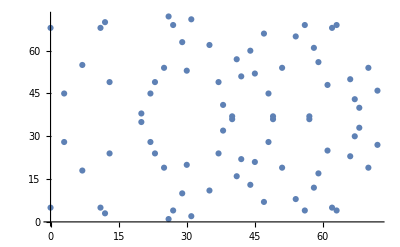

```mathematica
ListPlot[g1]
```

```mathematica
ListPlot3D[g1]
```

-Graphics3D-

```mathematica
ListPointPlot3D[g1]
```

-Graphics3D-

```mathematica
Задание 4;
EllipticAdd[p_,a_,b_,c_,P_List,Q_List]:=
Module[{lam,x3,y3,P3},
    Which[
P=={O},Q,
Q=={O},P,
P[[1]]!=Q[[1]],
		  lam=Mod[(Q[[2]]-P[[2]])PowerMod[Q[[1]]-P[[1]],p-2,p],p];
		  x3=Mod[lam^2-a-P[[1]]-Q[[1]],p];
		  y3=Mod[-(lam(x3-P[[1]])+P[[2]]),p];
		  {x3,y3},
(P==Q)∧(P[[2]]==0),{O},
(P==Q)∧(P!={O}),
		 lam=Mod[ (3*P[[1]]^2+2a*P[[1]]+b)PowerMod[2P[[2]],p-2,p],p];
  	  x3=Mod[lam^2-a-P[[1]]-Q[[1]],p];
		  y3=Mod[-(lam(x3-P[[1]])+P[[2]]),p];
		  {x3,y3},
(P[[1]]==Q[[1]])∧(P[[2]]!=Q[[2]]),{O}]]
EllipticAdd[p, 0, a, b , {0,5},{3,28}]
```

{72,27}

```mathematica
Задание 5;
p2 = 11;
a2 = 0;
b2 = 6;
c2 = 3;
EllipticAdd[p2,a2,b2,c2, {4,6},{9,4}]
EllipticAdd[p2,a2,b2,c2, {9,4},{9,4}]
EllipticAdd[p2,a2,b2,c2, {4,6},{4,6}]
EllipticAdd[p2,a2,b2,c2, {4,6},{O}]
EllipticAdd[p2,a2,b2,c2, {4,6},{4,5}]
EllipticAdd[p2,a2,b2,c2, {O},{9,4}]
```

{3,9}

{7,6}

{4,5}

{4,6}

{O}

{9,4}

```mathematica
Задание 6;
```

```mathematica
Задание 7;
```

```mathematica
Clear[Pnt1];
Pnt = {9,4};
myFun[1] = Pnt;
myFun[n_] :=myFun[n] = EllipticAdd[p2, a2, b2, c2, Pnt, myFun[n-1]];
Table[myFun[n],{n, 1, 5}]
```

{{9,4},{7,6},{7,5},{9,7},{O}}

```mathematica
Pnt = {3, 28};
myFun2[1] = Pnt;
myFun2[n_] :=myFun2[n] = EllipticAdd[p, 0, a, b, Pnt, myFun2[n-1]];
myTable =Table[myFun2[n],{n, 1, 8}]
```

{{3,28},{66,23},{59,17},{68,33},{56,69},{37,49},{51,54},{7,55}}

```mathematica
EllipticPointMultiply[p_,a_,b_,c_, Q_, n_] :=
Module[{i=n - 1, q=Q, pl=p,al=a,bl=b,cl=c},
pnt=q;
While[i > 0, i--; q=EllipticAdd[pl,al,bl,cl, pnt, q]];
q
]
EllipticPointMultiply[p,0,a,b, {3,28}, 1]
```

{3,28}

```mathematica
ListLinePlot[myTable, PlotMarkers->{Automatic, 10}, LabelingFunction->(#1 &)] /. Line[x_]->{Arrowheads[Table[.05,7]], Arrow[x]}
```

-Graphics-

```mathematica
Задание 8;
```

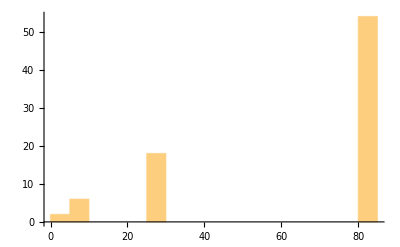
{{{27,18},{81,54},{9,6},{3,2}},-Graphics-}

```mathematica
s={};i=1;
For[j=1,j≤Length[g1],j++,{While[EllipticPointMultiply[p,0,a,b,g1[[j]],i]≠{O},i++],AppendTo[s,i],i=1}];
{Tally[s],Histogram[s,39]}
```